```mathematica
<<Utilities`CleanSlate`
```

```mathematica
CleanSlate[]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 164 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,URLUtilities`,PacletManager`,System`,Global`}

```mathematica
Clear["Global``*]
```

```mathematica
NSolve[x==Exp[-x],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.567143}}

```mathematica
NSolve[x==1-Exp[-x],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.}}

```mathematica
NSolve[0==-1+t+1.5t^2,t]
```

{{t→-1.21525},{t→0.548584}}

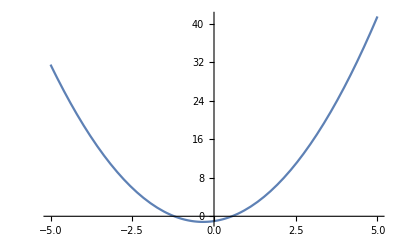

```mathematica
Plot[-1+t+1.5t^2,{t,-5,5}]
```

```mathematica
Clear[x,y,t]
```

```mathematica
s1 = NDSolve[{y''[t]==-10, y'[0]==0, y[0]==10},y,{t,0,5}]
```

{{y→InterpolatingFunction[…]}}

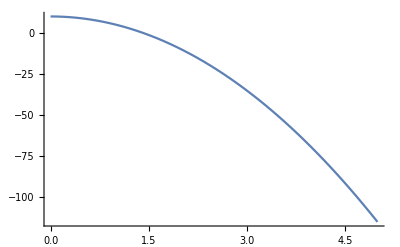

```mathematica
Plot[Evaluate[y[t]/.s1],{t,0,5},PlotRange->All]
```

```mathematica
Evaluate[y[t]/.s1]
```

{InterpolatingFunction[…][t]}

```mathematica
y
```

y

```mathematica
y[0]
```

10

```mathematica
y[5]
```

y[5]

```mathematica
s=NDSolve[{f'[x]==f[x]Cos[x+f[x]],f[0]==1},f,{x,0,30}]
```

{{f→InterpolatingFunction[…]}}

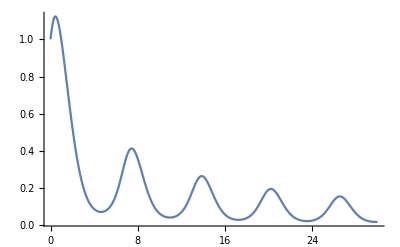

```mathematica
Plot[Evaluate[f[x]/.s],{x,0,30},PlotRange->All]
```